## Hexi—PS3—2025-01-21

### Exercises from EIWL3 Section 5

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Total[Range[10]^2]
```

385

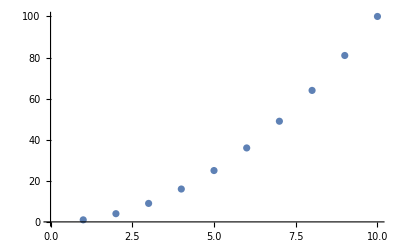

```mathematica
ListPlot[Range[10]^2]
```

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
IntegerLength[2^128]
```

39

```mathematica
First[IntegerDigits[2^32]]
```

4

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Max[IntegerDigits[2^20]]
```

8

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

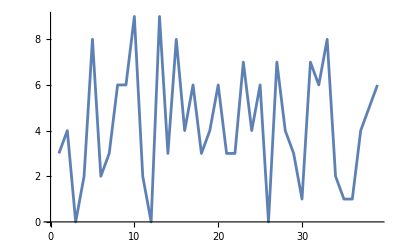

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
3*Range[10]
```

{3,6,9,12,15,18,21,24,27,30}

```mathematica
Range[10]*Range[10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Last[IntegerDigits[2^37]]
```

2

```mathematica
Part[Reverse[IntegerDigits[2^32]],2]
```

9

```mathematica
Total[IntegerDigits[3^126]]
```

234

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

```mathematica
{PieChart[IntegerDigits[2^20]], PieChart[IntegerDigits[2^40]],PieChart[IntegerDigits[2^60]]}
```

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

### Exercises from EIWL3 Section 6

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

```mathematica
Table[n^3, {n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

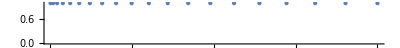

```mathematica
NumberLinePlot[Table[n^2,{n,20}]]
```

```mathematica
Range[2,20,2]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[n, {n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

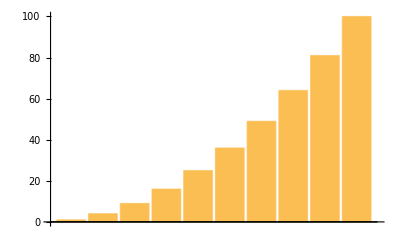

ListLinePlot::lpn: 100. is not a list of numbers or pairs of numbers.

```mathematica
BarChart[Table[n^2,{n,10}]]
```

```mathematica
IntegerDigits[Table[n^2,{n,10}]]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

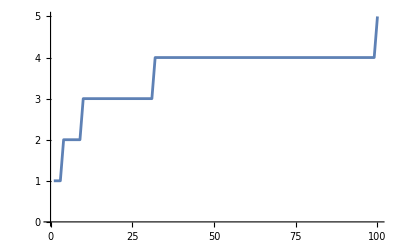

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

```mathematica
{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

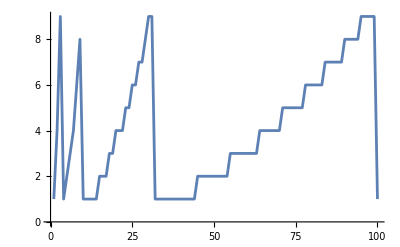

ListLinePlot::lpn: n^2 is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression n^2 cannot be used as a part specification.

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```

```mathematica
Table[n^3-n^2,{n,10}]
```

{0,4,18,48,100,180,294,448,648,900}

```mathematica
Table[n, {n,1,100, 2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
Table[n^2,{n,2,100,2}]
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

```mathematica
Range[-3,2]
```

{-3,-2,-1,0,1,2}

```mathematica
Table[Column[{i,i^2,i^3}],{i,1,20}]
```

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

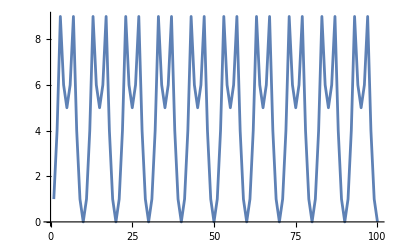

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^2]],{n,100}]]
```

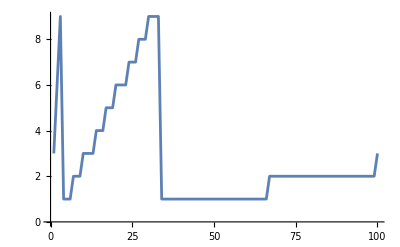

```mathematica
ListLinePlot[Table[First[IntegerDigits[3*n]], {n,100}]]
```

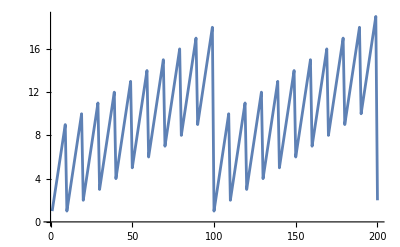

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n]],{n,200}]]
```

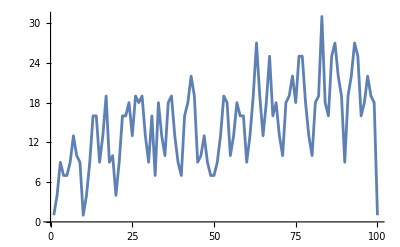

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n^2]],{n,100}]]
```

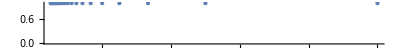

```mathematica
NumberLinePlot[Table[1/n, {n,20}]]
```

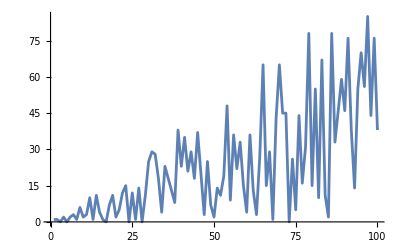

```mathematica
ListLinePlot[Table[RandomInteger[n],{n,100}]]
```

### Exercises from EIWL3 Section 7

```mathematica
{Red,Yellow, Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Column[{Red,Yellow, Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

```mathematica
Table[Hue[x],{x,0,1,0.02}]
```

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

```mathematica
Table[RGBColor[1,G,1],{G,0,1,0.02}]
```

{RGBColor[1, 0., 1],RGBColor[1, 0.02, 1],RGBColor[1, 0.04, 1],RGBColor[1, 0.06, 1],RGBColor[1, 0.08, 1],RGBColor[1, 0.1, 1],RGBColor[1, 0.12, 1],RGBColor[1, 0.14, 1],RGBColor[1, 0.16, 1],RGBColor[1, 0.18, 1],RGBColor[1, 0.2, 1],RGBColor[1, 0.22, 1],RGBColor[1, 0.24, 1],RGBColor[1, 0.26, 1],RGBColor[1, 0.28, 1],RGBColor[1, 0.3, 1],RGBColor[1, 0.32, 1],RGBColor[1, 0.34, 1],RGBColor[1, 0.36, 1],RGBColor[1, 0.38, 1],RGBColor[1, 0.4, 1],RGBColor[1, 0.42, 1],RGBColor[1, 0.44, 1],RGBColor[1, 0.46, 1],RGBColor[1, 0.48, 1],RGBColor[1, 0.5, 1],RGBColor[1, 0.52, 1],RGBColor[1, 0.54, 1],RGBColor[1, 0.56, 1],RGBColor[1, 0.58, 1],RGBColor[1, 0.6, 1],RGBColor[1, 0.62, 1],RGBColor[1, 0.64, 1],RGBColor[1, 0.66, 1],RGBColor[1, 0.68, 1],RGBColor[1, 0.7000000000000001, 1],RGBColor[1, 0.72, 1],RGBColor[1, 0.74, 1],RGBColor[1, 0.76, 1],RGBColor[1, 0.78, 1],RGBColor[1, 0.8, 1],RGBColor[1, 0.8200000000000001, 1],RGBColor[1, 0.84, 1],RGBColor[1, 0.86, 1],RGBColor[1, 0.88, 1],RGBColor[1, 0.9, 1],RGBColor[1, 0.92, 1],RGBColor[1, 0.9400000000000001, 1],RGBColor[1, 0.96, 1],RGBColor[1, 0.98, 1],RGBColor[1, 1., 1]}

```mathematica
Blend[{Pink, Yellow}]
```

RGBColor[1, 0.75, 0.25]

```mathematica
Table[Blend[{Yellow, Hue[x]}],{x,0,1,0.05}]
```

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

```mathematica
Style[Purple, 100]
```

RGBColor[0.5, 0, 0.5]

```mathematica
Table[Style[Red,x],{x,10,100,10}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
Style[999, 100, Red]
```

999

```mathematica
Table[Style[x^2,x],{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
colors={Red, Yellow, Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Part[colors,{1,3,2,3}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Part[colors,RandomInteger[{1,3},100]]
```

{RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Table[Style[Part[IntegerDigits[2^1000],n],3Part[IntegerDigits[2^1000],n]],{n,50}]
```

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}

### Exercises from EIWL3 Section 8



```mathematica
Graphics[RegularPolygon[3]]
```

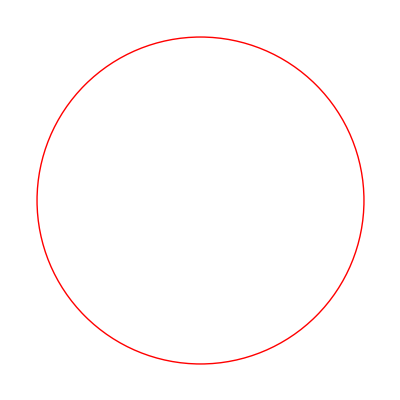

```mathematica
Graphics[Style[Circle[],Red]]
```

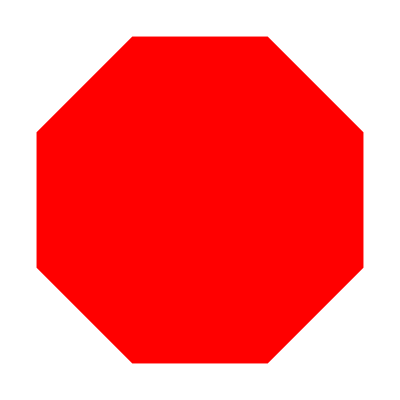

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```


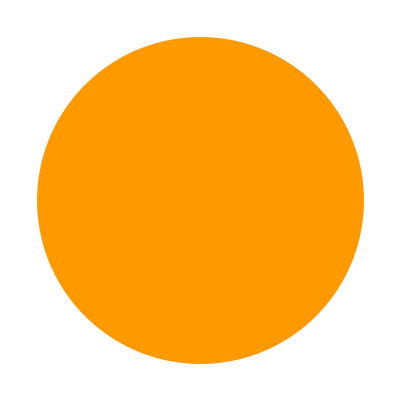
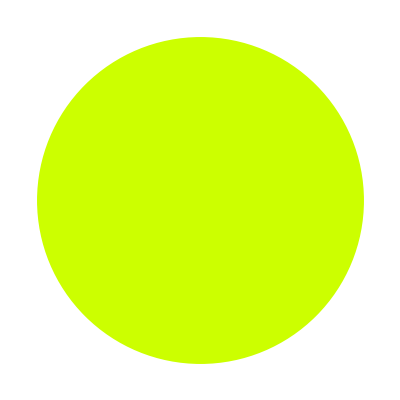
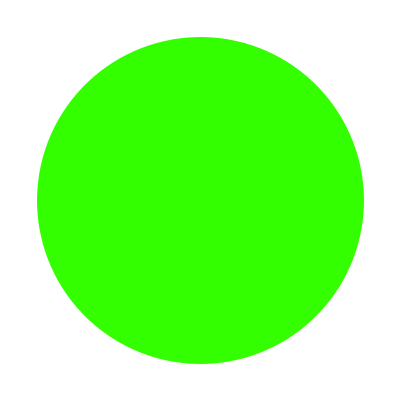
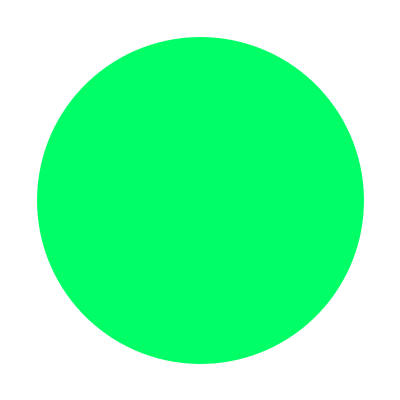
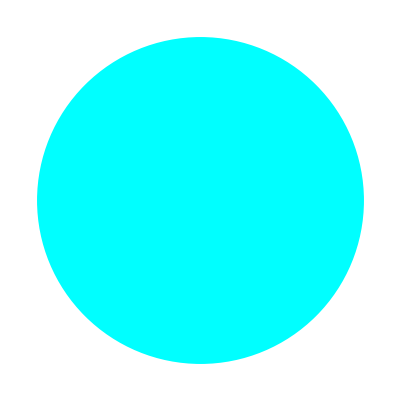
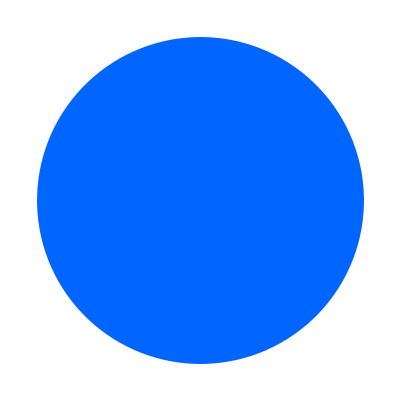
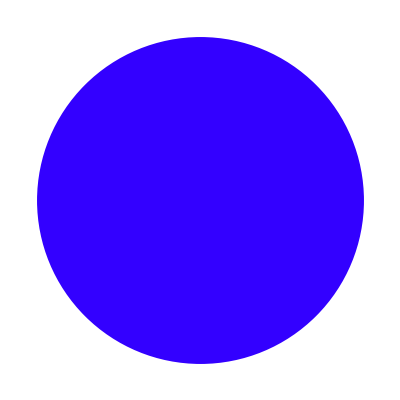
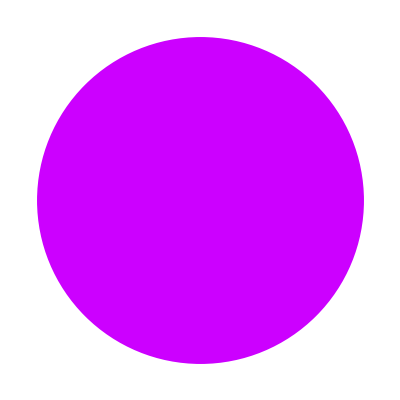
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
```

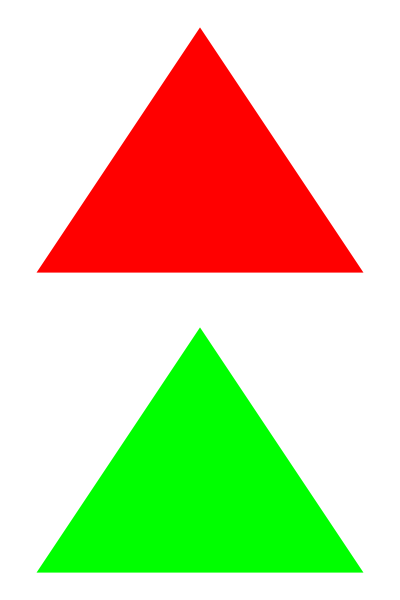

```mathematica
Column[{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}]
```

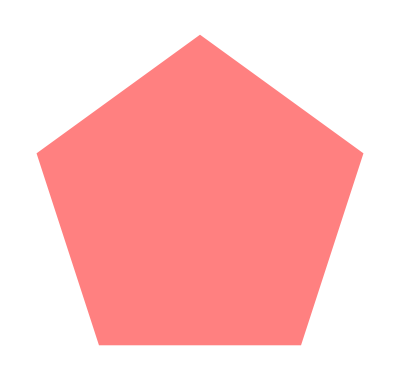
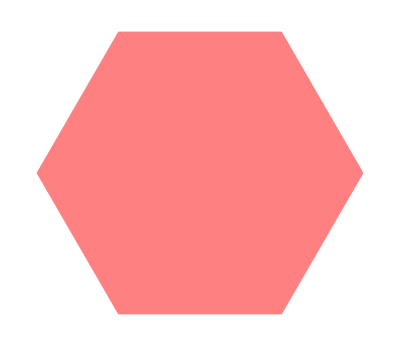
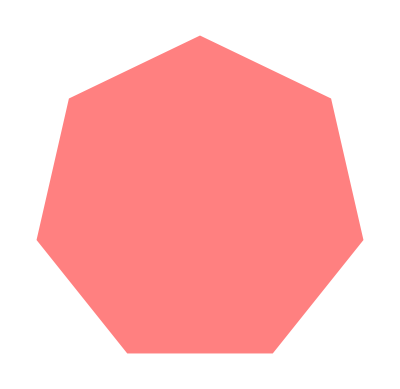
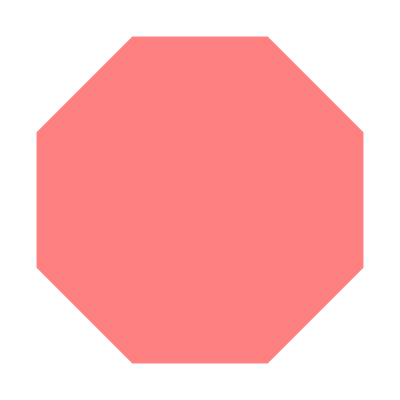
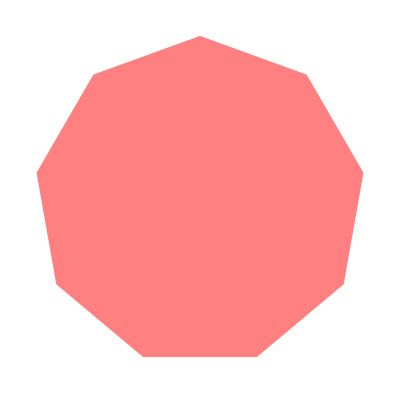
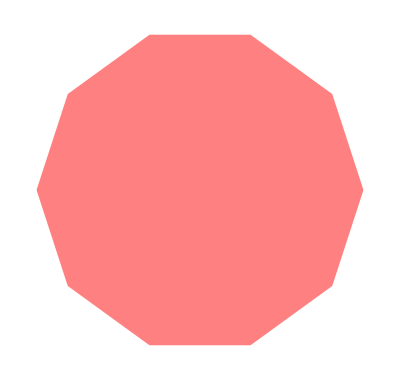

```mathematica
Table[Graphics[Style[RegularPolygon[n],Pink]],{n,5,10}]
```

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

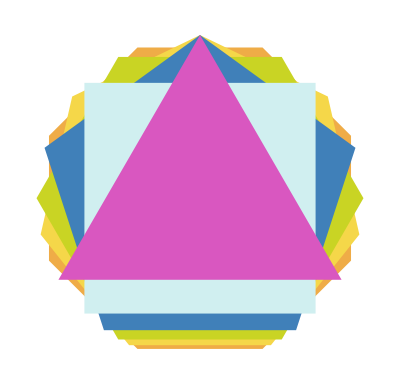

```mathematica
Graphics[Reverse[Table[Style[RegularPolygon[n],RandomColor[]],{n,3,8}]]]
```